# Data generation

```mathematica
SetDirectory[NotebookDirectory[]];
```

## Find out the max number of files there might be to import

[Header] and [Folder] should end in a ‘/’

```mathematica
Name="RunData";
Folder="GFlowSim/"<>Name<>"/";
Pos="general/Pos";
```

```mathematica
scale=150;
fps=15.;
```

```mathematica
maxRes=1024;
```

```mathematica
font=25;
```

```mathematica
animate=True;
verLists=True;
secData=True;
```

```mathematica
doCheck[list_]:=Quiet[If[list==$Failed,list={}]]
```

```mathematica
safeImport:=Function[{name},
Block[{data},
Quiet[data=Import[Folder<>name]];
Quiet[If[data==$Failed,data={}]];
data
]
]
```

## Check for data

```mathematica
If[Length[Import[Folder]]>1,isThereData=True,isThereData=False];
```

## Import data

Get the positions

```mathematica
(*
animate=True;
Quiet[If[Import[Folder<>Pos]==$Failed,animate=False]];
If[animate,
posdata=Import[Folder<>Pos<>"/data.csv"];
{dwidth,simdimensions,iters,ntypes}=posdata⟦1⟧;
bounds=posdata⟦2⟧;
vdata=posdata⟦3,2;;⟧;
sdata=posdata⟦4,2;;⟧;
idata=posdata⟦5,2;;⟧;
positions=posdata⟦6;;⟧;
]
*)
```

```mathematica
animate=False;
```

#### Get the snapshot

```mathematica
snapshot=safeImport["Snapshot/Snapshot0.csv"];
```

## Create Plots

```mathematica
SaveDirectory=Folder<>"Output/";
If[isThereData ,Quiet[CreateDirectory[SaveDirectory]],Null];
```

### Collect all graph type objects, and print out their data.

```mathematica
font=30;
Block[{plotnames,i,name,axis,data,min,max,img,ax,ay},
plotnames=Union[First/@StringSplit[safeImport["/plots"],{"/","."}]];
For[i=1,i≤Length[plotnames],++i,
name=plotnames⟦i⟧;
(* Get axis names *)
axis=safeImport["plots/"<>name<>"/axes.csv"];
If[Length[axis]>0,
ax=axis⟦1,1⟧;
ay=axis⟦2,1⟧;
(* Get data *)
data=safeImport["plots/"<>name<>"/"<>name<>".csv"];
(* Processing to know how to display data *)
min=Min[Last/@data];
max=Max[Last/@data];
If[max<0,max=0];
If[0<min,min=0];
img=ListLinePlot[data,PlotRange->{1.1min,1.1max},ImageSize->{1024,512},AspectRatio->0.5,PlotStyle->Black,Frame->True,FrameStyle->Thick,FrameTicksStyle->Directive[font,Black],FrameLabel->{Style[ax,font,FontFamily->"Times",Black],Style[ay,font,FontFamily->"Times",Black]}];
Export[Folder<>"Output/"<>name<>".pdf",img];
]
]
]
```

### Collect all multigraph type objects, and print out their data

```mathematica
Block[{plotnames,i,name,axis,data,ticks,slices,nslices,dataslices,min,max,colors,ax,ay},
plotnames=Union[First/@StringSplit[safeImport["/multigraph"],{"/","."}]];
For[i=1,i≤Length[plotnames],++i,
name=plotnames⟦i⟧;
(* Get axis names *)
axis=safeImport["multigraph/"<>name<>"/axes.csv"];

If[Length[axis]>0,
ax=axis⟦1,1⟧;
ay=axis⟦2,1⟧;
(* Get data *)
data=safeImport["multigraph/"<>name<>"/"<>name<>".csv"];
(* Split up data *)
ticks=First/@data;
slices=Table[#⟦i⟧&/@data,{i,2,Length[data⟦1⟧]}];
nslices=Length[slices];
dataslices=Table[Transpose[{ticks,slices⟦i⟧}],{i,1,nslices}];
(* Processing to know how to display data *)
min=Min[#⟦2;;⟧&/@data];
max=Max[#⟦2;;⟧&/@data];
If[max<0,max=0];
If[0<min,min=0];
(* Colors *)
colors=Table[RandomColor[],{nslices}];
img=ListLinePlot[dataslices,PlotRange->{1.1min,1.1max},ImageSize->{1024,512},AspectRatio->0.5,PlotStyle->colors,Frame->True,FrameStyle->Thick,FrameTicksStyle->Directive[font,Black],FrameLabel->{Style[ax,font,FontFamily->"Times",Black],Style[ay,font,FontFamily->"Times",Black]}];
Export[Folder<>"Output/"<>name<>".pdf",img];
(*
Print[(Total/@slices)/Length[slices⟦1⟧]];
Print[img];
*)
]
]
]
```

## Prob

```mathematica
DiskProb:=Function[{r,n,σ,L},
Block[{γ,ϕ},
γ=Re[2 √(1-r^2/4)];
ϕ=2σ n/L;
If[γ<1,(1-ϕ γ),
If[ϕ<1,Max[(1-ϕ)(1-ϕ/(n(1-ϕ))(γ-1))^n,0],0]
]
]
]
```

```mathematica
(*
polymerFrc=safeImport["general/TwoGroupStatistics/TwoGroupStatistics-force.csv"];
polymerVel=safeImport["general/TwoGroupStatistics/TwoGroupStatistics-vel.csv"];
*)
```

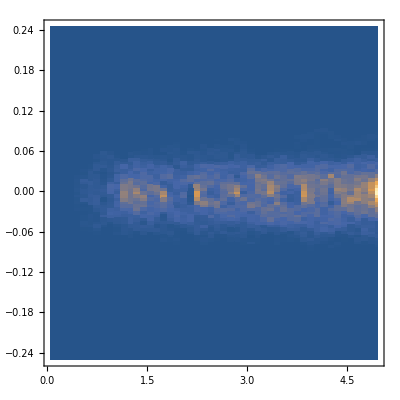

```mathematica
ListDensityPlot[polymerVel,InterpolationOrder->0,PlotRange->All]
```

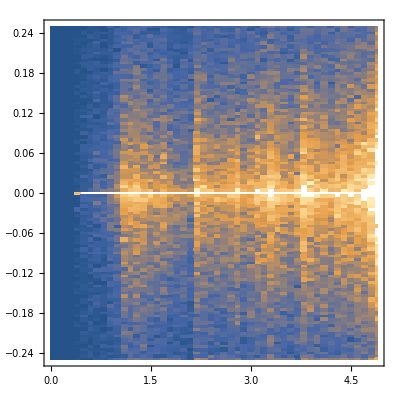

```mathematica
ListDensityPlot[polymerFrc,InterpolationOrder->0]
```

```mathematica
xvals=Union[First/@polymerFrc];
```

```mathematica
slices=Table[#⟦2;;3⟧&/@Select[polymerFrc,#⟦1⟧==xvals⟦i⟧&],{i,1,Length[xvals]}];
```

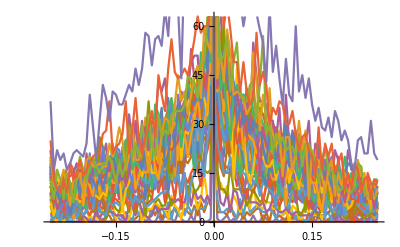

```mathematica
ListLinePlot[slices]
```

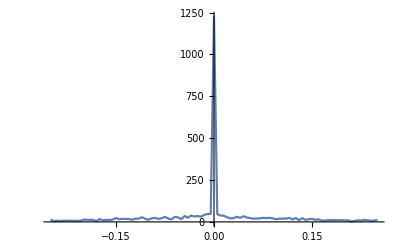

```mathematica
ListLinePlot[#⟦2;;3⟧&/@Select[polymerFrc,#⟦1⟧==3.5&],PlotRange->All]
```

### Resolution

```mathematica
res={maxRes,maxRes};
sg=Length[vdata]*simdimensions+1;
ty=Length[vdata]*simdimensions+Length[sdata]+1;
```

```mathematica
(* Add 1 for safety*)
Quiet[randCol=Table[RGBColor[RandomReal[],RandomReal[],RandomReal[]],{ntypes+1}]];
```

### Two and three dimensional circles/spheres

```mathematica
If[simdimensions≥3,dimeff=3,dimeff=2];
```

```mathematica
lj2[tr_,colchoice_:randCol]:={colchoice⟦tr⟦ty⟧+1⟧,Circle[tr⟦1;;dimeff⟧,tr⟦sg⟧],Disk[tr⟦1;;dimeff⟧,tr⟦sg⟧/2.5]}
```

```mathematica
obj2[tr_,colchoice_:randCol]:={colchoice⟦tr⟦ty⟧+1⟧,Disk[tr⟦1;;dimeff⟧,tr⟦sg⟧]}
obj3[tr_,colchoice_:randCol]:={colchoice⟦tr⟦ty⟧+1⟧,Sphere[tr⟦1;;dimeff⟧,tr⟦sg⟧]}
obj=If[dimeff>2,obj3,obj2];
```

#### Which graphics to use

```mathematica
GraphicsXd=Switch[simdimensions,1,Graphics,2,Graphics,3,Graphics3D];
```

### Animation

#### Particles

```mathematica
First[pos]⟦12⟧
```

First::normal: Nonatomic expression expected at position 1 in First[pos].

Part::partw: Part 12 of First[pos] does not exist.

First[pos]⟦12⟧

```mathematica
If[animate,
bnds=Table[{bounds⟦i⟧,bounds⟦i+simdimensions⟧},{i,1,simdimensions}];
pos=#⟦2;;⟧&/@positions;
If[dimeff<3,Obj=Disk,Obj=Sphere];
frames=Table[
{randCol⟦#⟦dwidth*i+ty⟧+1⟧,
EdgeForm[Thick],
Obj[#⟦dwidth*i+1;;dwidth*i+simdimensions⟧,
#⟦dwidth*i+sg⟧]},
{i,1,Length[#]/dwidth-1}]&/@pos;
gframes=GraphicsXd[#,ImageSize->{res},PlotRange->bnds]&/@frames;
]
```

```mathematica
If[animate,First@Timing[Export[SaveDirectory<>"output.avi",gframes,"CompressionLevel"->0]]]
```